```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]; 
Needs["HierarchicalClustering`"]
SetOptions[MatrixPlot,ImageSize->300{1,1}];
```

```mathematica
Module[{j=2.,k = 0.0677,xMin=0,xMax=j*(Pi/k),TMax=2000.,Bi=1.,M=35.1,Pr=7.02, Ga=0.,mult,Pm=0.3,S=100.,u,t,x,hSol,hSolp,hGrid,tRup},
mult=0.;
hSol= NDSolveValue[{D[u[t, x], t] == (-100)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         5*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}]

mult=1.;
hSolp= NDSolveValue[{D[u[t, x], t] == (-100)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         5*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}];

(*Plot[{hSol[TMax,x],hSolp[TMax,x]},{x,xMin,xMax},PlotRange->{0,4},BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel->{"Substrate(X-axis)","Film Profile [h(x,t)]"},ImageSize->Large,PlotStyle->{{Thick,Dashed,RGBColor[0.73,0.33,0.034]},{Thick,RGBColor[0.,0.1,0.01]}},PlotLegends->{"Zero Gravity without porosity","Zero Gravity with porosity"}]*)

(*With[{stepSize=0.5,end=xMax,fraction=0.45},
MatrixPlot[UnitStep[0.001-DistanceMatrix[hSol[fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome"]
MatrixPlot[UnitStep[0.001-DistanceMatrix[hSolp[fraction TMax,Range[xMin,end,stepSize]]]]]
]*)

(*With[{stepSize=0.3,end=xMax},
m0=Table[UnitStep[0.001-DistanceMatrix[hSol[fraction TMax,Range[xMin,end,stepSize]]]],{fraction,0,1,0.05}];
m1=Table[UnitStep[0.001-DistanceMatrix[hSolp[fraction TMax,Range[xMin,end,stepSize]]]],{fraction,0,1,0.05}];]*)
]
```

Set::write: Tag Times in 0. is Protected.

0. | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9 | 0.95 | 1.
0. | 47.1805 | 59.6657 | 65.4217 | 66.0908 | 61.8385 | 68.4982 | 75.5248 | 76.3151 | 87.3155 | 94.8683 | 98.4886 | 101.587 | 104.709 | 106.508 | 107.722 | 108.213 | 108.361 | 108.526 | 108.397 | 108.277

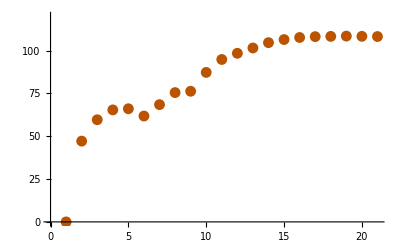

```mathematica
idx=Table[f,{f,0,1,0.05}];
tt=ParallelTable[Norm[m0[[i]]-m1[[i]],"Frobenius"]//N,{i,1,Dimensions[m0][[1]],1}];
TableForm[{idx,tt}]
p0x30=ListPlot[tt,PlotStyle->{RGBColor[0.73,0.33,0.0]},PlotRange->{All,{0,120}}]
```

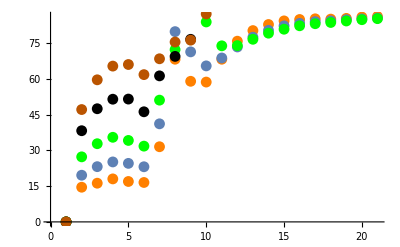

```mathematica
Show[p0x025,p0x05,p0x10,p0x20,p0x30]
```